```mathematica
setVariables[]
ΔE = 10000;
UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic // Diagonal // DiagonalMatrix) // N];
clearVariables[]
```

```mathematica
coreGateByλ[λ_, δE_] := (
setVariables[];

T1 = 5*10^-9;
T2 = 110*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;

Clear[Eamp, Bamp];

Ea =244;
Ba = .0318;

ωE = 3.3767399946666843*^10;
ωB = 3.365817946982966*^10;

Eamp[t_] := λ*Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := λ*Ba*cosWindow[t - T1, T2/5, T2];

ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12] + δE;

U = ConjugateTranspose[findEvolutionOperator2D[Hexact, Tmax]];
UU = U /. t->Tmax;

(*If[λ == 1,Print["XY gate with fidelity " <> ToString[fidelityXY[U /. t->Tmax]]]];
Print["core gate; parameters in lab frame ", gateDecompositionParameters[UU]];*)

clearVariables[];

UU
)

coreCalData = Table[{gateDecompositionParameters[coreGateByλ[λ, 0]][[2]], λ}, {λ, 0, 1, .05}];
ϕxFunction = Interpolation[coreCalData, Method->"Spline"];
coreGate[ϕx_, δE_] := coreGateByλ[ϕxFunction[ϕx], δE]
```

```mathematica
RzAngle[U_] := ArcTan[Re[U[[2, 2]]/U[[1, 1]]], Im[U[[2, 2]]/U[[1, 1]]]]
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)

RzByTime[T_?NumericQ,δE_] := (
statusString = "Error of " <> ToString[δE] <> "V/m"; 

setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;
Tmax = T;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] + δE // N;

U= findEvolutionOperator2D[Hexact, Tmax];

UU = U /. t->Tmax;

clearVariables[];

UU
)

RzCalData = Table[{RzAngle[RzByTime[tt, 0]], tt}, {tt, 0, 25*10^-9, 1*10^-9}];
RzCalData[[All, 1]] = unravel[RzCalData[[All, 1]]];
ϕzFunction = Interpolation[RzCalData, Method->"Spline"];
Rz[ϕz_, δE_] := RzByTime[ϕzFunction[ϕz], δE]
```

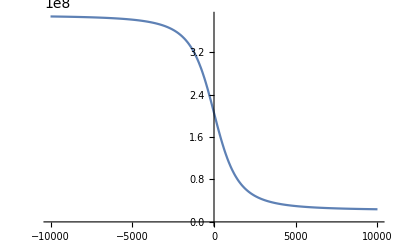

4.20131×10^-8

```mathematica
setVariables[]

Plot[δLab[2, 1], {ΔE, -10000, 10000}]

Clear[ΔE]
1/((δLab[2, 1] /. ΔE->10000))

clearVariables[]
```

```mathematica
cG = coreGate[π/2, 0];
cG // gateDecompositionParameters
(*rZg = Rz[2π - 5.859797, 0];
rZg // gateDecompositionParameters
cG.rZg // gateDecompositionParameters*)
```

{2.82768,1.57083,3.65155,1.11721,0.999958}

```mathematica
rZg = Rz[2π - 1, 0];
rZg // gateDecompositionParameters
```

{2.64159,0.,2.64159,1.27746,1.}

```mathematica
π/2 // N
```

1.5708